## Hydro+ Gubser test

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[ParentDirectory[wd]]
outputDir=root<>"/output";
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro

### plot styles

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[FontSize->FrameTicksFontSize,FontFamily->"Times",FontColor->Black],Directive[FontSize->FrameTicksFontSize,FontFamily->"Times",FontColor->Black]},FrameStyle->{Directive[AbsoluteThickness[1.1]],Directive[AbsoluteThickness[1.1]]},LabelStyle->{FontFamily->"Times",FontSize->FrameFontSize,FontColor->Black},BaseStyle->{FontFamily->"Times",FontSize->FrameFontSize,FontColor->Black},AspectRatio->2.5/3,ImageSize->300,PlotRange->All};
SetOptions[Plot,PlotOptions];
```

### time list

```mathematica
tlist={1.0,1.5,2.0,2.5};
clist={Red,Orange,Darker[Green],Blue};
```

```mathematica
legendlist=Table["τ = "<>ToString[PaddedForm[N[tlist[[i]]],{2,1},NumberPadding->{"","0"}]]<>" fm",{i,1,Length[tlist]}]
```

{τ = 1.0 fm,τ = 1.5 fm,τ = 2.0 fm,τ = 2.5 fm}

### data reader

```mathematica
Off[Interpolation::inhr];
varInt[t_,dir_,var_]:=Interpolation[Import[dir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{4,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

## Gubser hydro background

### equation of state

```mathematica
hbarc=0.197326938;
Nc=3;
Nf=2.5;
alphaB=0.145;
p0=(16+Nf*21/2)Pi^2/90;
fs=3*(p0+Nf/18*alphaB^2+Nf/(324*Pi^2)*alphaB^4)
gs=(Nf/9+Nf/(81*Pi^2)*alphaB^2)
hs=4/3*fs-alphaB^2*gs
```

13.9085

0.277844

18.5388

```mathematica
e[T_]=fs*T^4;
P[T_]=e[T]/3;
nB[T_]=alphaB*gs*T^3;
seq[T_]=hs*T^3;
```

### initial conditions

```mathematica
t0=1.0;
T0=1.2;
q=1.0;
```

### analytical solutions

```mathematica
rho[t_,r_,q_]:=ArcSinh[-(1-q^2*t^2+q^2*r^2)/(2q*t)];
theta[t_,r_,q_]:=ArcTan[(2q*Sqrt[r^2])/(1+q^2*t^2-q^2*r^2)];
kappa[t_,r_,q_]:=ArcTanh[(2*q^2*t*Sqrt[r^2])/(1+q^2*t^2+q^2r^2)];
urm[t_,r_]:=Sinh[kappa[t,r,q]];
utm[t_,r_]:=Cosh[kappa[t,r,q]];
```

```mathematica
Tm[t_,r_]:=T0/(t*(Cosh[rho[t,r,q]])^(2/3));
em[t_,r_]:=e[Tm[t,r]];
nm[t_,r_]:=nB[Tm[t,r]];
seqm[t_,r_]:=seq[Tm[t,r]];
```

## Hydro background test

### load numerical data

```mathematica
Clear[eInt,rhobInt,uxInt,utInt]
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,rhobInt,uxInt,utInt},{"e","rhob","ux","ut"}}];
```

### make plots

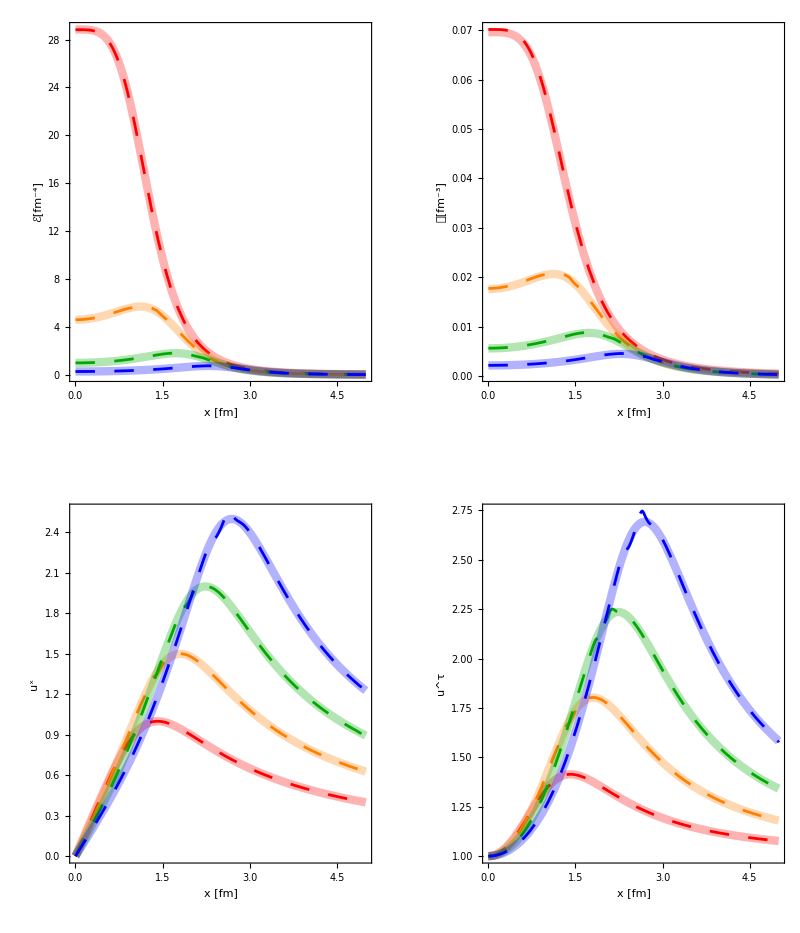

```mathematica
edPlot=Show[Table[Plot[{em[tlist[[i]],x],eInt[i-1][x,0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ℰ[fm^-4]"},ImageSize->300,AspectRatio->3.5/3];
rhodPlot=Show[Table[Plot[{nm[tlist[[i]],x],rhobInt[i-1][x,0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","𝒩[fm^-3]"},ImageSize->300,AspectRatio->3.5/3];
uxPlot=Show[Table[Plot[{urm[tlist[[i]],x],uxInt[i-1][x,0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^x"},ImageSize->300,AspectRatio->3.5/3];
utPlot=Show[Table[Plot[{utm[tlist[[i]],x],utInt[i-1][x,0,0]},{x,-0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^τ"},ImageSize->300,AspectRatio->3.5/3];
GraphicsGrid[{{edPlot,rhodPlot},{uxPlot,utPlot}}]
```

## Hydro+ slow modes

### plot setup

```mathematica
rm=5;
tm=5;
```

```mathematica
imagePadding1={{73,5},{2,7}};
imagePadding2={{73,5},{50,7}};
```

### correlation length

```mathematica
xi0=1.0;
Tc=0.16;
DeltaT=0.4*Tc;
Ws=0.3;
xi[T_]=xi0+2*Exp[-(T*hbarc-Tc)^2/(2*(Ws*DeltaT)^2)];
xit[t_,r_]=xi[Tm[t,r]];
```

### initial conditions

```mathematica
gammaQ0=0.9;
eqPhiQ0=1.0;
```

### parameterization

```mathematica
f2[x_]=1/(1+x^2);
fG[x_]=1+x^2;
F[t_,r_]=Tm[t,r]/Tm[t0,0.0];
gammaQm[t_,r_,{Q_}]=F[t,r]^-1*gammaQ0*Q^2*(xit[t,r]/xi0)^-2*fG[Q*xit[t,r]];
eqPhiQm[t_,r_,{Q_}]=F[t,r]^-3*eqPhiQ0*(xit[t,r]/xi0)^2*f2[Q*xit[t,r]];
```

### normalization factor

```mathematica
Subscript[C, λ]=(gammaQ0*Tm[t0,0.0])/2*hs^2/(alphaB*gs)
```

4606.67

## Slow modes test

### wave numbers

```mathematica
Q1=0.5;
Q2=1.2;
```

### load numerical data

```mathematica
Clear[eqQ0Int,eqQ1Int,Q0Int,Q1Int]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eqQ0Int,Q0Int,eqQ1Int,Q1Int},{"eqPhiQ0","phiQ0","eqPhiQ1","phiQ1"}}];
```

### numerical solutions

```mathematica
phiRatio1P=Show[Table[Plot[{Q0Int[i-1][r,0,0]/eqQ0Int[i-1][r,0,0]},{r,0,rm},PlotStyle->{AbsoluteThickness[2],clist[[i]],Dashing[Medium]}],{i,1,Length[tlist]}],FrameLabel->{"r [fm]","ϕ_Q/(ϕ̄)_Q"},ImageSize->300,AspectRatio->3.0/3,ImagePadding->imagePadding2,Epilog->Inset["(a)",{4.6,0.15}]];
plotText=Graphics[Text["Q = 0.5 fm^-1",{1.8,1.15},BaseStyle->{FontFamily->"Times",FontSize->20}]];
phiRatio1Pl=Show[phiRatio1P,plotText];
```

```mathematica
phiRatio2P=Show[Table[Plot[{Q1Int[i-1][r,0,0]/eqQ1Int[i-1][r,0,0]},{r,0,rm},PlotStyle->{AbsoluteThickness[2],clist[[i]],Dashing[Medium]},PlotLegends->Placed[LineLegend[{"τ = "<>ToString[PaddedForm[tlist[[i]],{2,1},NumberPadding->{"","0"}]]<>" fm"},LabelStyle-> {FontSize->15,FontFamily->"Times"},LegendMarkerSize->{{20,10}}],{0.75,0.65-0.11*i}]],{i,1,Length[tlist]}],FrameLabel->{"r [fm]"},ImageSize->300,AspectRatio->3.0/3,ImagePadding->imagePadding2,Epilog->Inset["(b)",{4.6,0.15}]];
plotText=Graphics[Text["Q = 1.2 fm^-1",{1.8,1.15},BaseStyle->{FontFamily->"Times",FontSize->20}]];
phiRatio2Pl=Show[phiRatio2P,plotText,PlotRange->{Automatic,{0.1,1.218}}];
```

### load semi-analytical solutions

```mathematica
Rdata=Import[root<>"/tests/HydroPlus-test/Gubser_PhiQ_0.5.dat"];
phiRatio1=Show[ListLinePlot[{Rdata[[All,{1,2}]],Rdata[[All,{1,3}]],Rdata[[All,{1,4}]],Rdata[[All,{1,5}]]},InterpolationOrder->3,PlotStyle->{{Red,AbsoluteThickness[4],Opacity[0.3]},{Orange,AbsoluteThickness[4],Opacity[0.3]},{Darker[Green],AbsoluteThickness[4],Opacity[0.3]},{Blue,AbsoluteThickness[4],Opacity[0.3]}}],PlotRange->{{0,5},Full}];
```

```mathematica
Rdata=Import[root<>"/tests/HydroPlus-test/Gubser_PhiQ_1.2.dat"];
phiRatio2=Show[ListLinePlot[{Rdata[[All,{1,2}]],Rdata[[All,{1,3}]],Rdata[[All,{1,4}]],Rdata[[All,{1,5}]]},InterpolationOrder->3,PlotStyle->{{Red,AbsoluteThickness[4],Opacity[0.3]},{Orange,AbsoluteThickness[4],Opacity[0.3]},{Darker[Green],AbsoluteThickness[4],Opacity[0.3]},{Blue,AbsoluteThickness[4],Opacity[0.3]}}],PlotRange->{{0,5},Full}];
```

### make plots

```mathematica
phiRatio1Plot=Show[phiRatio1Pl,phiRatio1];
```

```mathematica
phiRatio2Plot=Show[phiRatio2Pl,phiRatio2];
```

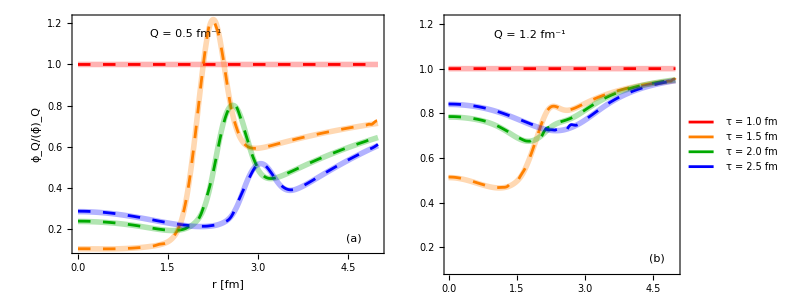

```mathematica
GubserXi=Grid[{{phiRatio1Plot,phiRatio2Plot}},Spacings->{0.8, 0}]
```

```mathematica
Export["Gubser_HydroPlus_validation.pdf",GubserXi]
```

Gubser_HydroPlus_validation.pdf